```mathematica
tri [x_]:=UnitTriangle[x];
boxcar[x_]:=UnitStep[x]-UnitStep[x-1];
gaussian[x_]:=(1/(2Pi))^(1/2)*Exp[-x^2/2];
erf[x_]:=∫_(-∞)^x gaussian[y]ⅆy;
step[x_]:=UnitStep[x];
estep[x_]:=Exp[-x]step[x];
h[t_,x_]:=(1/(2t)^(1/2))*gaussian[x*1/(2t)^(1/2)];
```

```mathematica
h[t,x]
```

(ⅇ^(-x^2/(4 t)))/(2 √π √t)

```mathematica
ode21[t_]:=∫_0^t ⅇ^(-2(t-τ))tri[τ]ⅆτ
```

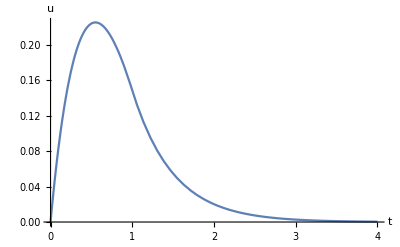

```mathematica
Plot[ode21[t],{t,0, 4},AxesLabel->{t,u}]
```

```mathematica
ode22[t_]:=1/2 NIntegrate[Sin[2(t-τ)]tri[τ],{τ,0,t}]
```

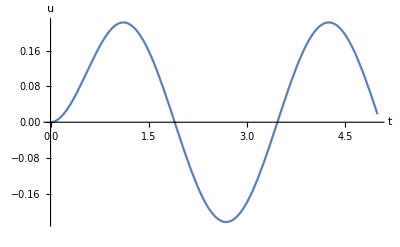

```mathematica
Plot[ode22[t],{t,0, 5},AxesLabel->{t,u}]
```

```mathematica
τ2[t_,x_]=x+t;
ξ2[t_,x_]=x-t;
```

```mathematica
pde23[t_,x_]:=1/2 Exp[-τ2/2]∫_0^τ2[t,x] Exp[s]tri[τ2[t,x]]tri[ξ2[t,x]]ⅆs
```

```mathematica
s=NDSolve[{D[u[t,x],t]+u[t,x]+D[u[t,x],x]==tri[x+t]tri[x-t],u[0,x]==0},u,{t,0,3},{x,-3,3}];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

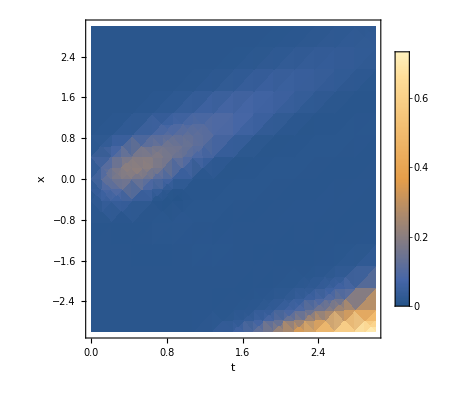

```mathematica
DensityPlot[Evaluate[u[t,x]/.s],{t,0,3},{x,-3,3}, PlotRange->All, FrameLabel->{t,x},PlotLegends->Automatic,PerformanceGoal->"Quality"]
```

```mathematica
Plot3D[Evaluate[u[t,x]/.s],{t,0,3},{x,-5,5}, PlotRange->All,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
pde24[t_,x_]:=1/4∫_0^t ∫_(x-2(t-τ))^(x+2(t-τ)) tri[y]tri[τ]ⅆyⅆτ
```

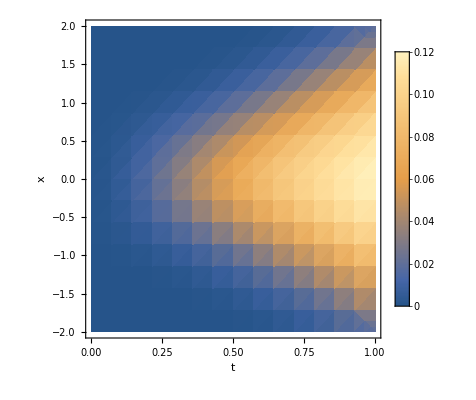

```mathematica
DensityPlot[pde24[t,x],{t,0,3},{x,-3, 3},PerformanceGoal->"Quality",FrameLabel->{t,x},PlotLegends->Automatic]
```

```mathematica
pde25[t_,x_]:=NIntegrate[NIntegrate[(tri[y]tri[τ-2])h[t-τ,x-y],{y,-∞,∞}],{τ,0,t}]
```

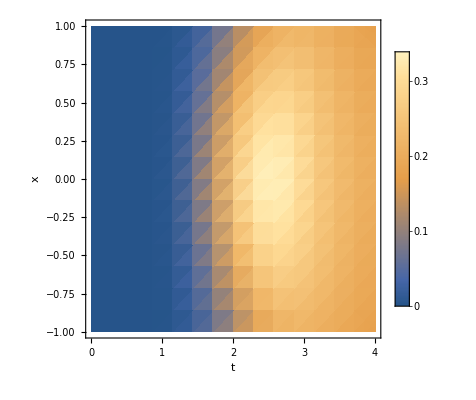

```mathematica
DensityPlot[pde25[t,x],{t,0,4},{x,-1, 1},PerformanceGoal->"Quality",FrameLabel->{t,x},PlotLegends->Automatic]
```